# A Matrix Formulation of Doubly-Recursive Functions

This essay presents a way to represent the doubly-recursive function f(n)=n-f(f(n-2)) as a function with only one level of recursion by using linear algebra.

## Regular Function

```mathematica
f[n_]:=f[n]=n-f[f[n-2]];
f[1]=1;
f[2]=1;
```

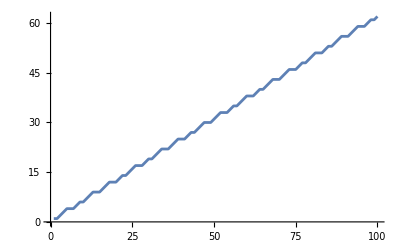

```mathematica
ListLinePlot[Table[f[i], {i, 1, 100}]]
```

## Representation

Instead of implementing a function based on a number n, I will instead implement it on the nth basis vector e_n. So instead of mapping n to f(n), this new function with map the nth basis vector to the f(n)th basis vector: F(e_n)=e_(f(n))
Because we are only dealing with basis vectors, and matrices represent a transformation of basis vectors, we can define a matrix M which will transform some finite number of n-basis vectors into f(n)-basis vectors.

#### Examples

(Note: For the most part, I will use superscripts to denote the dimension of a matrix. So M^(k×l) is a k by l matrix and M^k is a matrix with an input dimension of k.)
M^2 = (1 | 1
0 | 0), because f(1) = 1 and f(2) = 1, so M^2 takes e_1 to e_1 and e_2 to e_1.
 M^4 = (1 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1
0 | 0 | 0 | 0), which maps the first four unit vectors to the first four terms of the sequence {1, 1, 2, 3}
 M^8 = (1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0), which maps the first eight unit vectors to the first eight terms of the sequence {1, 1, 2, 3, 4, 4, 4, 5}

Generally,

```mathematica
matFromSequence[L_List] := Transpose[Table[
  If[And[n > 0, n <= Length[L]],
    UnitVector[Length[L], n],
    ConstantArray[0, Length[L]]
  ], {n, L}]]
```

```mathematica
matFromSequence[f/@Range[16]]//MatrixForm
```

(1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

By representing the transformation in this way, we can see that F(e_n)=M^n*e_n, so M is basically the characteristic matrix of F.

## Implementation

In order to find a form of F, we need to state the formula for f in terms of matrix multiplications.

f(n) = n - f(f(n - 2))
In other words, if you take n, subtract 2, compose map it under f twice, then subtract n from it, you get your output.

Let S_n be a matrix which takes any basis vector e_i to e_(i-n).
Let R_n be a matrix which takes any basis vector e_i to e_(n-i).

In order to subtract 2 from n, we do S_2*e_n.
In order to map it under F, we apply M*M*S_2*e_n.
In order to take that result from n, we apply R_n*M*M*S_2*e_n.
Thus, M=R_n*M*M*S_2 and F(e_n)=M*e_n=R_n*M*M*S_2*e_n.

#### Explicit Formulae for S and R

As an example, look at the form of S_2^8:

```mathematica
matFromSequence[(#-2)&/@Range[8]]//MatrixForm
```

(0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

Generally, S_n^d=(0^(d-n×n) | I^(d-n×d-n)
0^(n×n) | 0^(n×d-n)), where I is the identity matrix and 0 is the zero matrix.

```mathematica
matS[n_,d_]:=
ArrayFlatten[
{{0,IdentityMatrix[{d-n, d-n}]},
{ConstantArray[0,{n,n}],0}}
]
```

```mathematica
matS[2, 8]//MatrixForm
```

(0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

As an example, look at the form of R_7^8:

```mathematica
matFromSequence[(7-#)&/@Range[8]]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

Generally, R_n^d=(A^(n-1×n-1) | 0^(n-1×d-n+1)
0^(d-n+1×n-1) | 0^(d-n+1×d-n+1)), where A is the antidiagonal matrix (the mirror of I).

```mathematica
matA[n_]:=Reverse[IdentityMatrix[n]]
```

```mathematica
matR[n_,d_]:=
ArrayFlatten[
{{matA[n-1], 0},
{0, ConstantArray[0, {d-n+1, d-n+1}]}}
]
```

```mathematica
matR[7, 8]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

## Recursive Formulation

The form of M which I presented relies on itself in the same dimension, so it cannot be used as a formula to compute M:  M^d=R_n^d*M^d*M^d*S_2^d. However, because we are shifting all of the input basis vectors by 2, the final two columns of M actually will have no effect. We can therefore replace M^d with M^(d-2), as long as we change some dimensions of other matrices so that it still works.

Let D be a matrix similar to S, except that it has dimensions D_n^(d-n×d) instead of S_n^(d×d).
Generally, D_n^d=(0^(d-n×n) | I^(d-n×d-n)).

```mathematica
matD[n_, d_]:=ArrayFlatten[{{ConstantArray[0, {d-n, n}], IdentityMatrix[{d-n, d-n}]}}]
```

Let E be a matrix which elongates it’s input by n dimensions.
Generally, E_n^d = (I^(d×d)
0^(n×d)).

```mathematica
matE[n_, d_]:=ArrayFlatten[{{IdentityMatrix[{d, d}]}, {ConstantArray[0, {n, d}]}}]
```

Therefore, we can instead write M^d = E_2^(d-2)*R_n^(d-2)*M^(d-2)*M^(d-2)*D_2^d, Combining the M*M, we get this singularly recursive formula for M:
M^d = E_2^(d-2)*R_n^(d-2)*(M^(d-2))^2*D_2^d.
Note that there is still an n in the subscript of R. Because of this new formulation with changing dimensions, if we make d equal to n (i.e., the input basis vector must always be the last basis vector of it’s dimensionality), then we can replace R_n with R_d as long as we are careful with dimensions.

#### Implementation

```mathematica
matMtry2[d_]:=matFromSequence[Table[
If[Or[j==1,j==2], 1, 
j-Dot[Range[d], (With[{prevMatM=matMtry2[d-2]},matE[2, d-2].prevMatM.prevMatM.matD[2, d]]).UnitVector[d, j]]
], {j, 1, d}]]
```

```mathematica
matMtry2[14]//MatrixForm
```

(1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
FfromMatrix[n_]:=Range[n].matMtry2[n].UnitVector[n, n]
```

```mathematica
FfromMatrix[6]
```

4

```mathematica
FfromMatrix/@Range[14]
```

{1,1,2,3,4,4,4,5,6,6,7,8,9,9}

```mathematica
d=8
matD[2, d]//MatrixForm
```

8

(0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)